```mathematica
SetDirectory["C:/Users/Ian/Desktop/Persistent Homology DNA/Output/SE"]
```

C:\Users\Ian\Desktop\Persistent Homology DNA\Output\SE

```mathematica
SetDirectory["C:\\Users\\David\\Dropbox\\De Bruijn Graphs\\PersistentHomology\\Persistent Homology DNA\\Output\\FullPlexSE\\"]
```

C:\Users\David\Dropbox\De Bruijn Graphs\PersistentHomology\Persistent Homology DNA\Output\FullPlexSE

```mathematica
(*Don't do this at dimension 1 since there are a ton of small intervals in the begining, and we know there should just be a single connected component.*)
```

```mathematica
MaxFiltrationSize=3;
Dim=3;
```

```mathematica
(*Quiet[] is so it won't throw an error if the betti numbers etc. are missing*)
```

```mathematica
Quiet[SampleAAllEndpoints=Import["Acidothermus_cellulolyticus_11B_uid58501.dim3BarcodeEndpointStruct.mat"];]
```

```mathematica
(*Order is: Dim0, Dim1, Dim2, Betti numbers*)
```

```mathematica
SampleADim1EndPoints=SampleAAllEndpoints[[1,Dim,1]]/.{∞->MaxFiltrationSize}
```

{{3.28,3.36},{1.04,1.12},{0.96,1.04}}

```mathematica
(*Sometimes there are no intervals*)
```

```mathematica
If[Not[SameQ[Head[SampleADim1EndPoints],List]],SampleADim1EndPoints={};]
```

```mathematica
Quiet[SampleBAllEndpoints=Import["Aciduliprofundum_boonei_T469_uid43333.dim3BarcodeEndpointStruct.mat"];]
```

```mathematica
SampleBDim1EndPoints=SampleBAllEndpoints[[1,Dim,1]]/.{∞->MaxFiltrationSize}
```

Transpose[Partition[{},0.]]

```mathematica
If[Not[SameQ[Head[SampleBDim1EndPoints],List]],SampleBDim1EndPoints={};]
```

```mathematica
Length[SampleADim1EndPoints]
Length[SampleBDim1EndPoints]
```

3

0

```mathematica
(*Add points to make them the same length*)
```

```mathematica
If[Length[SampleADim1EndPoints]<Length[SampleBDim1EndPoints],SampleADim1EndPoints=Join[Table[-i,{i,1,Length[SampleBDim1EndPoints]-Length[SampleADim1EndPoints]}],SampleADim1EndPoints];]
If[Length[SampleBDim1EndPoints]<Length[SampleADim1EndPoints],SampleBDim1EndPoints=Join[Table[-i,{i,1,Length[SampleADim1EndPoints]-Length[SampleBDim1EndPoints]}],SampleBDim1EndPoints];]
```

```mathematica
Length[SampleADim1EndPoints]
Length[SampleBDim1EndPoints]
```

3

3

```mathematica
numIntervals=Length[SampleADim1EndPoints];
```

```mathematica
(*Make sure the distances to the diagonal points are appropriate (shortest distance)*)
```

```mathematica
dist=If[Length[#1]==0,Norm[#2-Projection[#2,{1,1}]],If[Length[#2]==0,Norm[#1-Projection[#1,{1,1}]],Norm[#1-#2]]]&
```

If[Length[#1]==0,Norm[#2-Projection[#2,{1,1}]],If[Length[#2]==0,Norm[#1-Projection[#1,{1,1}]],Norm[#1-#2]]]&

```mathematica
(*Tack on a unique identifier to take care of the problem of repeat intervals (otherwise this leads to two different intervals being identified as one)*)
```

```mathematica
edges=Flatten[Table[Rule[{SampleADim1EndPoints[[i]],"a"<>ToString[i]},{SampleBDim1EndPoints[[j]],"b"<>ToString[j]}],{i,1,Length[SampleADim1EndPoints]},{j,1,Length[SampleBDim1EndPoints]}],1];
```

```mathematica
edgeWeights=Table[dist[edges[[i,1,1]],edges[[i,2,1]]],{i,1,Length[edges]}];
```

```mathematica
(*Could also do bottom up instead of top down. -Last->Last and <numIntervals -> ≥numIntervals*)
```

```mathematica
sortedEdges=SortBy[Thread[List[edges,edgeWeights]],-Last[#]&];
```

```mathematica
i=1;
toolow=0;
toohigh=Length[sortedEdges];
If[Length[sortedEdges]==0,0,If[Length[sortedEdges]==1,sortedEdges[[1,2]],While[toohigh≠ toolow+1,
If[Length[FindIndependentEdgeSet[Graph[sortedEdges[[i;;,1]],EdgeWeight->sortedEdges[[i;;,2]]]]]<numIntervals,toohigh=i,toolow=i
];
i=Ceiling[(toolow+toohigh)/2]
]
]
]
sortedEdges[[i-1,2]]
```

0.0565685

```mathematica
i
```

4

```mathematica
(*Visualize what's going on*)
```

```mathematica
(*Full Graph*)
```

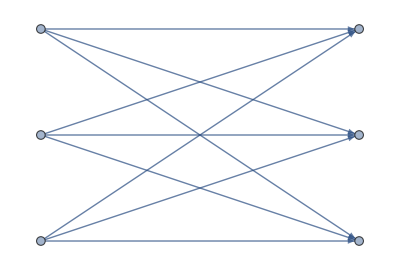

```mathematica
Graph[edges,GraphLayout->"BipartiteEmbedding"]
```

```mathematica
(*After deleting the ith vertex. Can't do a maximal matching*)
```

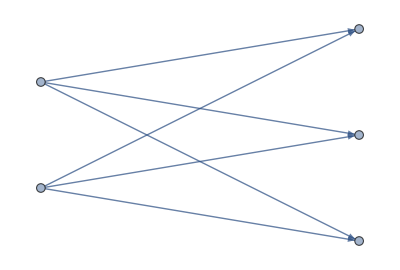

```mathematica
Graph[sortedEdges[[i;;,1]],EdgeWeight->sortedEdges[[i;;,2]],GraphLayout->"BipartiteEmbedding"]
```

```mathematica
(*But can do it with i-1*)
```

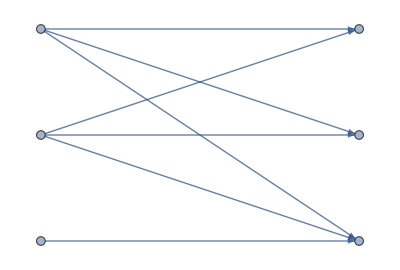

```mathematica
Graph[sortedEdges[[i-1;;,1]],EdgeWeight->sortedEdges[[i-1;;,2]],GraphLayout->"BipartiteEmbedding"]
```

```mathematica
(*All together for server*)
```

```mathematica
(*fileNames=FileNames["*.dim3BarcodeEndpointStruct.mat"];*)
LaunchKernels[45]
(*Run in the FullPlexSE directory as:nohup/local/cluster/Wolfram/Mathematica/10.0/bin/math-script../../Scripts/BottleneckDistanceFaster.m>../../Scripts/MathematicaNohup.txt 2>&1&*)
(*fileNames=FileNames["*.dim3BarcodeEndpointStruct.mat"];*)
fileNames=ReadList["../../Data/SmallOrganismsCompleted.txt","String"];
fileNames=#<>".dim3BarcodeEndpointStruct.mat"&/@fileNames;
dist=If[Length[#1]==0,Norm[#2-Projection[#2,{1,1}]],If[Length[#2]==0,Norm[#1-Projection[#1,{1,1}]],Norm[#1-#2]]]&;
MaxFiltrationSize=8;
Dim=1;
Dim=Dim+1;
numFiles=Length[fileNames];
indicies=Flatten[Table[If[i<j,{i,j}],{i,1,numFiles},{j,i+1,numFiles}],1];
vals=ParallelTable[Quiet[SampleAAllEndpoints=Import[fileNames[[index[[1]]]]];];
SampleADim1EndPoints=SampleAAllEndpoints[[1,Dim,1]]/.{∞->MaxFiltrationSize};
If[Not[SameQ[Head[SampleADim1EndPoints],List]],SampleADim1EndPoints={};];
Quiet[SampleBAllEndpoints=Import[fileNames[[index[[2]]]]];];
SampleBDim1EndPoints=SampleBAllEndpoints[[1,Dim,1]]/.{∞->MaxFiltrationSize};
If[Not[SameQ[Head[SampleBDim1EndPoints],List]],SampleBDim1EndPoints={};];
If[Length[SampleADim1EndPoints]<Length[SampleBDim1EndPoints],SampleADim1EndPoints=Join[Table[-i,{i,1,Length[SampleBDim1EndPoints]-Length[SampleADim1EndPoints]}],SampleADim1EndPoints];];
If[Length[SampleBDim1EndPoints]<Length[SampleADim1EndPoints],SampleBDim1EndPoints=Join[Table[-i,{i,1,Length[SampleADim1EndPoints]-Length[SampleBDim1EndPoints]}],SampleBDim1EndPoints];];
numIntervals=Length[SampleADim1EndPoints];
edges=Flatten[Table[Rule[{SampleADim1EndPoints[[i]],"a"<>ToString[i]},{SampleBDim1EndPoints[[j]],"b"<>ToString[j]}],{i,1,Length[SampleADim1EndPoints]},{j,1,Length[SampleBDim1EndPoints]}],1];
edgeWeights=Table[dist[edges[[i,1,1]],edges[[i,2,1]]],{i,1,Length[edges]}];
sortedEdges=SortBy[Thread[List[edges,edgeWeights]],-Last[#]&];
i=1;
toolow=0;
toohigh=Length[sortedEdges];
If[Length[sortedEdges]==0,outDist=0,If[Length[sortedEdges]==1,outDist=sortedEdges[[1,2]],While[toohigh≠toolow+1,If[Length[FindIndependentEdgeSet[Graph[sortedEdges[[i;;,1]],EdgeWeight->sortedEdges[[i;;,2]]]]]<numIntervals,toohigh=i,toolow=i];i=Ceiling[(toolow+toohigh)/2]];
outDist=sortedEdges[[i-1,2]];]];
outDist,{index,indicies},Method->"FinestGrained"];
outDists=Normal[SparseArray[Thread[Rule[indicies,vals]],{numFiles,numFiles}]];
(*Export["../../Test/TestDim"<>ToString[Dim]<>"BottleneckDistances.mat",outDists];*)
Export["../../Output/FullPlexSEDim"<>ToString[Dim]<>"BottleneckDistances.mat",outDists];
```